```mathematica
Y=397.903 10^9;
σ=0.29;
α=4.3 10^-6;
```

```mathematica
ArrZ=Table[ii,{ii,0,2.1,0.02}];
```

```mathematica
ArrT=Table[ii,{ii,0,1000,20}];
```

```mathematica
Int1=Table[Interpolation[Table[{ArrZ[[ii]]/1000,Tn[ArrT[[jj]],ArrZ[[ii]],0]},{ii,1,Length[ArrZ],1}]],{jj,1,Length[ArrT],1}];
```

```mathematica
M1=-α Table[NIntegrate[Y/(1-σ)Int1[[jj]][x](x-0.0021/2),{x,0,0.0021}],{jj,1,Length[ArrT],1}];
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

```mathematica
M1I=Interpolation[Table[{ArrT[[jj]],M1[[jj]]},{jj,1,Length[ArrT],1}]]
```

InterpolatingFunction[…]

```mathematica
M[t_,r_]:=2^(-(r/(20/2))^2)M1I[t]
```

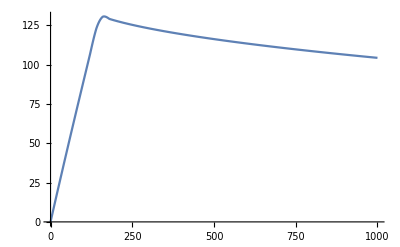

```mathematica
Plot[M[t,0],{t,0,1000},PlotRange->All]
```